```mathematica
Clear["Global`*"]
Quiet[<<Combinatorica`]
```

```mathematica
s= SparseArray[{
{1,2}->5,{1,3}->10,
{2,3}->3,
{3,1}->2,{3,4}->5,
{4,1}->6
},{4,4},Infinity];
S=Normal[s];
S//MatrixForm
```

(∞ | 5 | 10 | ∞
∞ | ∞ | 3 | ∞
2 | ∞ | ∞ | 5
6 | ∞ | ∞ | ∞)

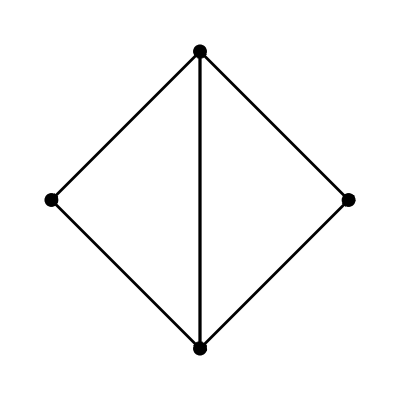

```mathematica
g1 =FromAdjacencyMatrix[S,EdgeWeight,Type->Directed];
ShowGraph[g1,VertexLabel-> True]
```

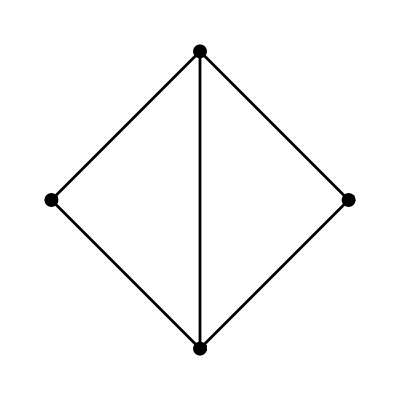

```mathematica
g2 =FromAdjacencyMatrix[S,EdgeWeight];
ShowGraph[g2,VertexLabel-> True]
```

```mathematica
ShortestPath[g1,1,3]
```

{1,2,3}

```mathematica
s= SparseArray[{
{1,2}->5,{1,3}->10,{1,6}->10,
{2,3}->3,{2,5}->6,
{3,4}->2,{3,5}->3,{3,6}->4,
{4,5}->2,{4,6}->5
},{6,6},Infinity];
S=Normal[s];
S//MatrixForm
```

(∞ | 5 | 10 | ∞ | ∞ | 10
∞ | ∞ | 3 | ∞ | 6 | ∞
∞ | ∞ | ∞ | 2 | 3 | 4
∞ | ∞ | ∞ | ∞ | 2 | 5
∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞)

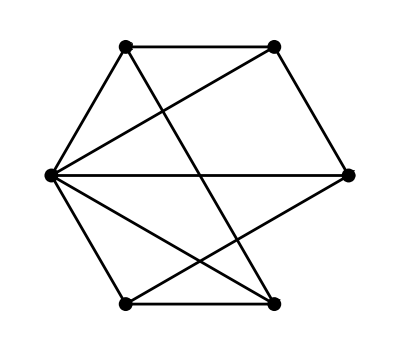

```mathematica
gs =FromAdjacencyMatrix[S,EdgeWeight];
ShowGraph[gs,VertexLabel-> True]
```

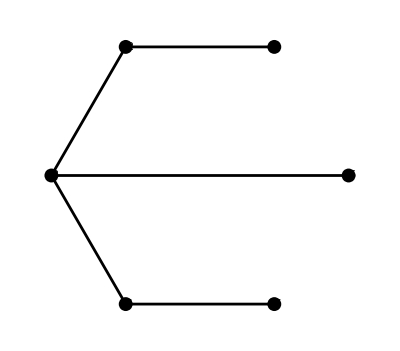

```mathematica
ShowGraph[MinimumSpanningTree[gs],VertexLabel-> True]
```

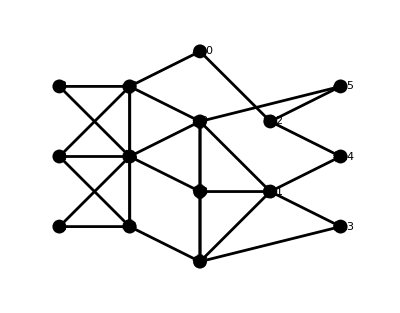

```mathematica
s=SparseArray[{
{1,4}->45,{1,5}->47,
{2,4}->53,{2,5}->50,{2,6}->48,
{3,5}->41,{3,6}->49,
{4,6}->30,{4,7}->49,
{5,8}->40,{5,9}->48,
{6,4}->53,{6,9}->47,{6,10}->39,
{7,13}->50,{7,11}->45,{7,8}->51,
{8,7}->51,{8,11}->46,{8,9}->47,
{9,8}->47,{9,11}->52,{9,15}->49,
{10,12}->48,
{11,13}->47,{11,14}->57,
{12,14}->53,{12,15}->43},
{15,15},Infinity];
S=Normal[s];
gs =FromAdjacencyMatrix[S,EdgeWeight,Type->Directed];
ShowGraph[RankedEmbedding[gs,{{1,2,3},{4,5,6},{7,8,9,10},{11,12},{13,14,15}}],VertexLabel-> True]
```

```mathematica
net =NetworkFlow[gs,1,13]
```

92

```mathematica
netegde = NetworkFlow[gs,1,13,Edge]
```

{{{1,4},45},{{1,5},47},{{4,7},45},{{5,8},40},{{5,9},7},{{7,13},50},{{8,7},5},{{8,11},35},{{9,11},7},{{11,13},42}}

```mathematica
{#[[1,1]]-> #[[1,2]], #[[2]]}&/@netegde  //TableForm
```

1→4 | 45
1→5 | 47
4→7 | 45
5→8 | 40
5→9 | 7
7→13 | 50
8→7 | 5
8→11 | 35
9→11 | 7
11→13 | 42